## Fundamental constants

## Physical constants used throughout the book

```mathematica
(*First, we clear all previous definitions to ensure a clean start. *)

ClearAll["Global`*"];
```

```mathematica
cSI=Quantity[299792458,"Meters"/"Seconds"]; (*Speed of light*)
```

```mathematica
cCGS=UnitConvert[cSI,"Centimeters"/"Seconds"];
```

```mathematica
ergPerJoule=Quantity[10^7,"Ergs"/"Joules"];
```

```mathematica
(*Planck constant and related quantities*)
hSI=Quantity[6.62606957*10^-34,"Joule"*"Seconds"];
```

```mathematica
hbarSI=hSI/(2*Pi);
```

```mathematica
hCGS=UnitConvert[hSI,"Ergs"*"Seconds"];
```

```mathematica
ElectronVoltsPerJoule=Quantity[6.24150934*10^18,"Electronvolts"/"Joule"];
```

```mathematica
heV=hSI*ElectronVoltsPerJoule;
```

```mathematica
Quantity[4.135667510864479*^-15,"Electronvolts" "Seconds"]
```

4.13567×10^-15 s eV

```mathematica
ElectronVoltsPerJoule hSI
```

4.13567×10^-15 s eV

```mathematica
(*Boltzmann constant*)
kBSI=Quantity[1.3806488*10^-23,"Joules"/"Kelvins"];
```

```mathematica
kBCGS=UnitConvert[kBSI,"Ergs"/"Kelvins"];
```

```mathematica
kBeVperK=UnitConvert[kBSI,"Electronvolts"/"Kelvins"];
```

```mathematica
WienDisplacementConstantHzperK=Quantity[5.878925757646824946*10^10,"Hertz"/"Kelvins"];
```

```mathematica
(*Newtonian gravitational constant*)
GSI=Quantity[6.673848*10^-11,"Meters"^3/"Kilograms"/"Seconds"^2];
```

```mathematica
mPerKg = GSI/cSI^2; (* Conversion to geometrized units *)
```

```mathematica
(* Vacuum permittivity (epsilon0SI) this name has changed*)
epsilon0SI = 1/(4*Pi*Quantity[8.988*10^9, "Newtons"*"Meters"^2/"Coulombs"^2];);
```

```mathematica
(*Radiation density constant*)
RadiationDensityConstantSI=(8*Pi^5*kBSI^4)/(15*hSI^3*cSI^3)//UnitSimplify;
```

```mathematica
RadiationDensityConstantCGS=(8*Pi^5*kBCGS^4)/(15*hCGS^3*cCGS^3)//UnitSimplify;
```

```mathematica
(*Cosmological constants*)
secPerDay=Quantity[86400,"Seconds"/"Days"];
```

```mathematica
secPerYear=Quantity[365.2425,"Days"/"Years"]*secPerDay;
```

```mathematica
1.0006643835616438
```

1.00066

```mathematica
parsecSI=Quantity[3.08567758149137*10^16,"Meters"];
```

```mathematica
lightyearSI=Quantity[365.2425,"Days"]*secPerDay*cSI;
```

```mathematica
(*Hubble parameter*)
h=0.7; (*Example dimensionless Hubble parameter*)
```

```mathematica
hubbleSI=Quantity[(100*h*10^3)/(3.08567758149137*10^22),"Seconds"^-1];
```

```mathematica
Quantity[2.2685455026110534*^-18,1/("Seconds")]
```

2.26855×10^-18 per second

```mathematica
(*Electron*)
ChargeElectronSI=Quantity[1.602*10^-19,"Coulombs"];
```

```mathematica
ElectronMassSI=Quantity[9.109*10^-31,"Kilograms"];
```

```mathematica
(*Proton and Neutron*)
MassProtonSI=Quantity[1.672621778*10^-27,"Kilograms"];
```

```mathematica
MassNeutronSI=Quantity[1.67492735*10^-27,"Kilograms"];
```

```mathematica
MassProtoneV=UnitConvert[MassProtonSI*cSI^2,"Electronvolts"];
```

```mathematica
MassProtonGU=MassProtonSI*GSI/cSI^2;
```

```mathematica
(*Earth*)
earthMassSI=Quantity[5.9736*10^24,"Kilograms"];
```

```mathematica
earthRadiusSI=Quantity[6.371*10^6,"Meters"];
```

```mathematica
earthEquatorialRadiusSI=Quantity[6378137,"Meters"];
```

```mathematica
earthOmegaSI=2*Pi/(Quantity[23*3600+56*60+4.091,"Seconds"]);
```

```mathematica
earthEquatorSpeedSI=earthEquatorialRadiusSI*earthOmegaSI;
```

```mathematica
(*Moon*)
MoonDistSI=Quantity[384399000,"Meters"];
```

```mathematica
MoonMassSI=Quantity[7.3477*10^22,"Kilograms"];
```

```mathematica
(*Sun*)
MassSunSI=Quantity[1.98855*10^30,"Kilograms"];
```

```mathematica
RadiusSunSI=Quantity[6.958*10^8,"Meters"];
```

```mathematica
SunLuminositySI=Quantity[3.828*10^26,"Watts"];
```

## Chapter 1: Special relativity

## Exercise 1.1(a,c,e,g)

### Convert the following to units in which c=1, expressing everything in terms of [m] and [kg]

```mathematica
(*1.1(a) 10[J] in natural units*)
AnswerCh1Ex1a=N[10/cSI^2,3]
```

```mathematica
(*1.1(c) hbar [J s] in natural units*)
```

```mathematica
AnswerCh1Ex1c=N[hbarSI/cSI]
```

```mathematica
(*1.1(e) 30 x 10^3[kg m/s] in natural units*)
```

```mathematica
AnswerCh1Ex1e=N[30000/cSI]
```

```mathematica
(*1.1(g) Density of water, 1000[kg/m^3] in natural units*)
```

Here we do not need to convert the units because there are no seconds to convert to meters! Later, in Chapter 8, we will see how to convert kilograms to meters.

## Exercise 1.2 (a,c,e):

### Convert the following from natural units (c=1) to SI units:

```mathematica
(*1.2(a) v=10^-2*)
AnswerCh1Ex2a=0.01*cSI;
```

```mathematica
0.01 cSI
```

```mathematica
(*1.2(c) Time, t=10^18*)
AnswerCh1Ex2c=N[Quantity[10^18,"Meters"]/cSI,4];
```

```mathematica
Quantity[3.3356409519815204957557671447`4.*^9,"Seconds"]
```

```mathematica
(*1.2(e) Acceleration a=10 m^-1*)
```

```mathematica
AnswerCh1Ex2e=N[Quantity[10,"Meters"^-1]*cSI^2,4];
```

```mathematica
Quantity[8.9875517873681764`4.*^17,("Meters")/("Seconds")^2]
```

## Exercise 1.3 (c,g,h,i):

```mathematica
(* Exer. 1.3(a) The worldline of a particle, e.g. a clock, stationary in this coordinate system. *)Graphics[{Black,Thick,Line[{{1,-1},{1,3}}]},PlotRange->{{-1,3},{-1,3}},Axes->True,AxesLabel->{"x","t"}]
```

```mathematica
(* Exer. 1.3(b) The worldline of a particle moving at a tenth of the speed of light along the x axis *)
Plot[10*(x-0.5),{x,-1,3},PlotRange->{-1,3},PlotStyle->Black,AxesLabel->{"x","t"}]
```

```mathematica
(* Exer 1.3(c): The axes of an observer moving at half the speed of light along the x axis *)(* xbarLabel=OverBar["x"];
tbarLabel=OverBar["t"]; *)
xbarLabel=OverBar["x"];
tbarLabel=OverBar["t"];

AnswerEx1o3c=Plot[{2*x,1/2*x},{x,-1,4},PlotRange->{{-1,3.5},{-1,4}},PlotStyle->Directive[Black,AbsoluteThickness[0.5],Solid],AxesLabel->{"x","t"},(*Keep regular axes labels*)PlotLabels->{Placed[tbarLabel,Top],Placed[xbarLabel,Right]},(*These would now label the curves*)LabelStyle->{FontFamily->"Times",FontSize->18,FontSlant->"Italic"},AspectRatio->1]
```

```mathematica
OverBar["x"]
```

```mathematica
AnswerEx1o3cbis=Plot[{2*x,1/2*x},{x,-1,4},PlotRange->{{-1,4},{-1,4}},(*Adjusted to show the full graph and labels*)PlotStyle->Directive[Black,AbsoluteThickness[0.5],Solid],AxesLabel->{"x","t"},
BaseStyle->Directive[Black,FontFamily->"Times",FontSlant->"Italic",FontSize->18],
TicksStyle->Directive[Black,FontFamily->"Helvetica",FontSlant->"Plain",FontSize->16],(*Applies to the numbers on the ticks (0,1,2,...,6) and (-1.0,-0.5,...)*)
Epilog->{Text[Style[xbarLabel,FontFamily->"Times",FontSlant->"Italic",FontSize->18],{3.6,1.5}](*Absolute coordinates*),Text[Style[tbarLabel,FontFamily->"Times",FontSlant->"Italic",FontSize->18],{1.6,3.6}]},AspectRatio->1]
```

```mathematica
Plot[{2 x,x/2},{x,-1,4},PlotRange->{{-1,4.5},{-1,4.5}},PlotStyle->Black,AxesLabel->{"x","t"},PlotLabels->{Placed[tbarLabel,Top],Placed[xbarLabel,Right]},AspectRatio->1]
```

```mathematica
(* Exer 1.3(d): Interval Delta s^2 = -1. These events are time-like separated from the origin. *)Plot[{Sqrt[x^2+1],-Sqrt[x^2+1]},{x,-3,3},PlotStyle->Black,AxesLabel->{"x","t"},AspectRatio->1]
```

```mathematica
(* Exer 1.3(e): Interval Delta s^2 = 1. These events are space-like separated from the origin *)Plot[{Sqrt[x^2-1],-Sqrt[x^2-1]},{x,-3,3},PlotStyle->Black,AxesLabel->{"x","t"},AspectRatio->1]
```

```mathematica
(* Exer.  1.3(f) Calibration ticks at 1m intervals along the x-bar and t-bar axes of (c). Below, The thin dotted lines are the invariant hyperbolae. The 6 hyperbolae crossing the t-axes have squared interval from the origin of {1,4,9} m^2,and thus mark of {-3,-2,-1,+1,+2,+3}m along both time axes.The 6 hyperbolae that cross the x-axes have negative squared interval {-1,-4,-9} m^2 and thus mark off {-3,-2,-1,1,2,3}m. *)
```

```mathematica
Plot[{2*x,(1/2)*x,Sqrt[x^2+1],-Sqrt[x^2+1],Sqrt[2^2+x^2],-Sqrt[2^2+x^2],Sqrt[3^2+x^2],-Sqrt[3^2+x^2],Sqrt[x^2-1],-Sqrt[x^2-1],Sqrt[x^2-2^2],-Sqrt[x^2-2^2],Sqrt[x^2-3^2],-Sqrt[x^2-3^2]},{x,-3.75,3.75},PlotRange->{{-3.75,3.75},{-3.75,3.75}},PlotStyle->{Directive[Black,AbsoluteThickness[2],Solid],(*2*x,using Dashed for visual distinctness as solid black is default for the first line*)Directive[Black,AbsoluteThickness[2],Solid],(*(1/2)*x*)Directive[Black,AbsoluteThickness[1],Dotted],(*Sqrt[x^2+1]*)Directive[Black,AbsoluteThickness[1],Dotted],(*-Sqrt[x^2+1]*)Directive[Black,AbsoluteThickness[1],Dotted],(*Sqrt[2^2+x^2]*)Directive[Black,AbsoluteThickness[1],Dotted],(*-Sqrt[2^2+x^2]*)Directive[Black,AbsoluteThickness[1],Dotted],(*Sqrt[3^2+x^2]*)Directive[Black,AbsoluteThickness[1],Dotted],(*-Sqrt[3^2+x^2]*)Directive[Black,AbsoluteThickness[1],Dotted],(*Sqrt[x^2-1]*)Directive[Black,AbsoluteThickness[1],Dotted],(*-Sqrt[x^2-1]*)Directive[Black,AbsoluteThickness[1],Dotted],(*Sqrt[x^2-2^2]*)Directive[Black,AbsoluteThickness[1],Dotted],(*-Sqrt[x^2-2^2]*)Directive[Black,AbsoluteThickness[1],Dotted],(*Sqrt[x^2-3^2]*)Directive[Black,AbsoluteThickness[1],Dotted] (*-Sqrt[x^2-3^2]*)},AxesLabel->{"x","t"},AspectRatio->1]
```

```mathematica
(* Exer. 1.3(g): Locus of points with interval from the origin, delta s^2 = 0. *)
```

```mathematica
AnswerEx1o3g=Plot[{x,-x},{x,-1,4},PlotStyle->{Directive[Black,AbsoluteThickness[0.5],Dashed] ,Directive[Black,AbsoluteThickness[0.5],Dashed]},AxesLabel->{"x","t"},BaseStyle->{FontFamily->"Helvetica",FontSize->14},(*For general plot text like numbers on axes*)LabelStyle->{FontFamily->"Times",FontSize->18,FontSlant->"Italic"},(*For AxesLabel text*)PlotRange->{{-1,4},{-2,4}},AspectRatio->Automatic (*To ensure correct scaling,as mentioned in previous answers*)]
```

```mathematica
AnswerEx1o3h=Plot[2,{x,-1,4},PlotStyle->Directive[Black,AbsoluteThickness[0.75],Solid] ,AxesLabel->{"x","t"},BaseStyle->{FontFamily->"Helvetica",FontSize->14},(*For general plot text like numbers on axes*)LabelStyle->{FontFamily->"Times",FontSize->18,FontSlant->"Italic"},(*For AxesLabel text*)PlotRange->{{-1,4},{-1,4}},AspectRatio->Automatic ]
```

```mathematica
AnswerEx1o3i=Plot[4/Sqrt[3]+(x-2/Sqrt[3])*(1/2),{x,-1,4},PlotStyle->Directive[Black,AbsoluteThickness[1.5],Solid] ,AxesLabel->{"x","t"},BaseStyle->{FontFamily->"Helvetica",FontSize->14},(*For general plot text like numbers on axes*)LabelStyle->{FontFamily->"Times",FontSize->18,FontSlant->"Italic"},(*For AxesLabel text*)PlotRange->{{-1,4},{-1,4}},AspectRatio->Automatic ]
```

```mathematica
AnswerEx1o3hyperbole=Plot[Sqrt[2^2+x^2],{x,-1,4},PlotStyle->Directive[Black,AbsoluteThickness[0.5],Dotted] ,AxesLabel->{"x","t"},BaseStyle->{FontFamily->"Helvetica",FontSize->14},(*For general plot text like numbers on axes*)LabelStyle->{FontFamily->"Times",FontSize->18,FontSlant->"Italic"},(*For AxesLabel text*)PlotRange->{{-1,4},{-1,4}},AspectRatio->Automatic ]
```

```mathematica
Show[AnswerEx1o3cbis,AnswerEx1o3g,AnswerEx1o3h,AnswerEx1o3i,AnswerEx1o3hyperbole]
```

## Exercise 1.14

### Suppose that the velocity v of referential Obar relative to O is small, |v| << 1. Show that the time dilation, Lorentz contraction and velocity-addition formulae can be approximated by, respectively: (see textbook)

#### (a) Time dilation (including relative error (d)):

```mathematica
(* Define the true function for the Lorentz factor. Note naming convention:
capital letters for the first letter is reserved for Mathematica build-in 
functions. *)
lfTrue[v_] := 1/Sqrt[1 - v^2]

(* Series expansion of Ftrue around v = 0 up to v^4 *)
Series[lfTrue[v], {v, 0, 5}]

(* We can understand the series expansion above by compting the 
first few terms of a Taylor series about v=0. E.g. the v^2, v^3, and v^4 
 *)
 (* The first term is simply the function evaluated at v=0*)
term1 = lfTrue[0]
(* The second (non-zero) term contains the second-order derivative of the function 
evaluated at v=0 *)
d2 = D[lfTrue[v], {v, 2}] // Simplify;
term2 = (d2 /. v -> 0)/Factorial[2]
(* The third order term contains the third-order derivative of the function 
. When evaluated at v=0 this term (and all odd-order terms) vanish !*)
d3 = D[lfTrue[v], {v, 3}] // Simplify;
d3 /. v -> v
term3 = (d3 /. v -> 0)/Factorial[3]
(* The fourth order term contains the fourth-order derivative of the function 
. When evaluated at v=0 this term (and all even-order terms) are non-zero *)
d4 = D[lfTrue[v], {v, 4}] // Simplify;
d4 /. v -> v
term4 = (d4 /. v -> 0)/Factorial[4]

(* Alternative: Taylor expansion of the Lorentz factor using x = v^2 . 
This leads to the same result but more directly, avoiding the odd power terms
that evaluated to zero above. *)
(* Here is the function definition for the Lorentz factor *)
lf[x_] := 1/Sqrt[1 - x]
(* Below we define the first derivative with respect to x:*) 
d1x = D[lf[x], {x}] // Simplify;
(* which we evaluate with x = v^2 to show its functional dependence *)
d1x /. x -> v^2
(* and then we evaluate it at x=0 to get the constant for that term in the Taylor series *) 
term1x = d1x /. x->0
(* Below we repeat the above steps for the second derivative, including the
2! in the denominator *)
d2x = D[lf[x], {x, 2}] // Simplify;
d2x /. x -> v^2
term2x = (d2x /. x -> 0)/Factorial[2]

(* Approximation to order v^2 *)
lfApprox[v_] := 1 + (1/2)*v^2

(* Finally, the result we are asked for: Relative error at v = 0.1 *)
RelativeError = N[(lfTrue[0.1] - lfApprox[0.1])/lfTrue[0.1]]
```

#### (b) Length contraction (including relative error (d))

```mathematica
(* The (exact) Length contraction factor, the factor to multiply the proper length to get
the contracted length observed when the rod is moving.  *)
lcfTrue[v_] := Sqrt[1 - v^2];
lcfTrue[x] /. x-> v
```

```mathematica
(* Find the Taylor series expansion for the above function to order 5 *)
Series[lcfTrue[v], {v, 0, 5}]
```

```mathematica
(* Length contraction factor: approximation to order v^2, by inspection of the
above result *)
lcfApprox[v_] := 1 - (1/2)*v^2;
lcfApprox[x] /. x-> v
```

```mathematica
(* The result we are asked for: Relative error at v = 0.1  *)
RelativeError = N[(lcfTrue[0.1] - lcfApprox[0.1])/lcfTrue[0.1]]
```

#### (c) Velocity addition (including relative error (d))

```mathematica
(* The (exact) velocity addition formula  *)
wprimeTrue[v_, w_] := (v + w)/(1 + v*w)
wprimeTrue[v,w]
```

```mathematica
(* Define the approximate expression *)
wprimeApprox[v_, w_] := (v + w)*(1 - v*w)
wprimeApprox[v, w]
```

```mathematica
(* Compute the relative error at v = 0.1, w = 0.1 *)
RelativeError = N[(wprimeTrue[0.1, 0.1] - wprimeApprox[0.1, 0.1])/wprimeTrue[0.1, 0.1]]
```

## Chapter 5: Preface to curvature

## Exercise 5.21(b) Draw the coordinate curves for the coordinates (a, λ) obtained from transformation (t,x) using Schutz Eq.(5.96)

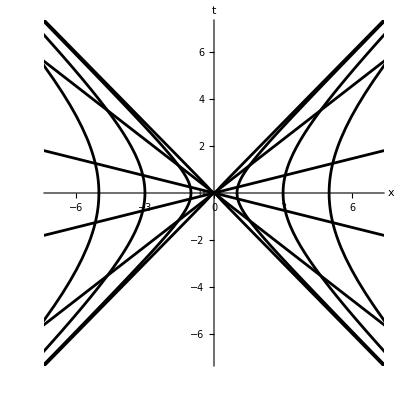

```mathematica
(*Solution to Schutz, Exercise 5.21: Plotting Rindler Coordinates*)

(*This notebook converts a Maple plotting command from the solution to Exercise 5.21 into Mathematica. 
The goal is to plot the coordinate curves for Rindler space, which are defined by the parametric equations:*)
(*t = a * Sinh[λ]*)
(*x = a * Cosh[λ]*)
(*The plot shows lines of constant `a` (hyperbolas) and lines of constant `λ` 
(straight lines through the origin).*)

(*2. Defining the Parametric Equations*)

(*In Maple, the variables `t` and `x` were defined using `:=`. In Mathematica, it's best 
to define them as functions that depend on the parameters `a` and `λ`.*)


t[a_, λ_] := a*Sinh[λ];
x[a_, λ_] := a*Cosh[λ];


(*3. Creating the Plot*)

(*The Maple `plot` command contains a list of many different curves to draw. The most 
direct way to replicate this in Mathematica is to create a list of `ParametricPlot` 
commands, one for each curve, and then combine them using `Show`.*)
(*We will also translate the Maple plot options (like `color`, `view`, and `labels`) 
into their Mathematica equivalents (`PlotStyle`, `PlotRange`, and `AxesLabel`).*)

(* Create a list of all the individual plots *)
plotList = {
   (* Curves of constant 'a' (hyperbolas) *)
   ParametricPlot[{x[0.1, λ], t[0.1, λ]}, {λ, -5, 5},PlotStyle -> Black],
   ParametricPlot[{x[1, λ], t[1, λ]}, {λ, -3, 3},PlotStyle -> Black],
   ParametricPlot[{x[3, λ], t[3, λ]}, {λ, -2, 2},PlotStyle -> Black],
   ParametricPlot[{x[5, λ], t[5, λ]}, {λ, -2, 2},PlotStyle -> Black],
   ParametricPlot[{x[-0.1, λ], t[-0.1, λ]}, {λ, -5, 5},PlotStyle -> Black],
   ParametricPlot[{x[-1, λ], t[-1, λ]}, {λ, -3, 3},PlotStyle -> Black],
   ParametricPlot[{x[-3, λ], t[-3, λ]}, {λ, -2, 2},PlotStyle -> Black],
   ParametricPlot[{x[-5, λ], t[-5, λ]}, {λ, -2, 2},PlotStyle -> Black],
   
   (* Curves of constant 'λ' (straight lines) *)
   ParametricPlot[{x[a, 0.25], t[a, 0.25]}, {a, -50, 50},PlotStyle -> Black],
   ParametricPlot[{x[a, 1], t[a, 1]}, {a, -50, 50},PlotStyle -> Black],
   ParametricPlot[{x[a, -0.25], t[a, -0.25]}, {a, -50, 50},PlotStyle -> Black],
   ParametricPlot[{x[a, -1], t[a, -1]}, {a, -5, 5},PlotStyle -> Black]
   };

(* Combine all plots into a single graphic with styling *)
Show[plotList,
 PlotRange -> {{-7.1, 7.1}, {-7.1, 7.1}},
 PlotStyle -> Black,
 AxesLabel -> {"x", "t"},
 AxesStyle -> Directive[FontFamily -> "Times", Italic, 18],
 TicksStyle->Directive[Black,FontFamily->"Helvetica",FontSlant->"Plain",FontSize->14],
 Epilog->{Text[Style["(a)", FontFamily -> "Helvetica", FontSlant -> "Plain", 
    FontSize -> 14], {-5, 7.5}]}
 ]
(*For general plot text like numbers on axes*)
```

To find the slope of the straight lines, we note that t/x is tanh(lambda):

```mathematica
Tanh[0.25]
```

0.244919

```mathematica
N[Tanh[1]]
```

0.761594

For subplot B, we plot the 4 lines and just the single innermost hyperbola, and zoom in on the origin.

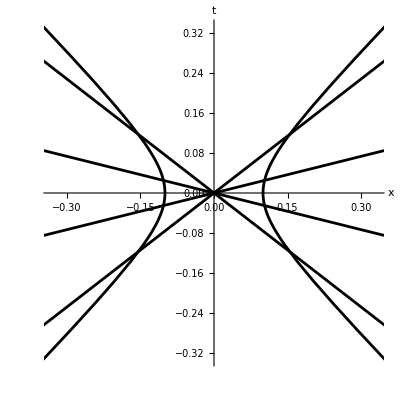

```mathematica
Show[plotList[[{1,5,9,10,11,12}]],
 PlotRange -> {{-1/3, 1/3}, {-1/3, 1/3}},
 PlotStyle -> Black,
 AxesLabel -> {"x", "t"},
 AxesStyle -> Directive[FontFamily -> "Times", Italic, 18],
 TicksStyle->Directive[Black,FontFamily->"Helvetica",FontSlant->"Plain",FontSize->14],
  Epilog -> {Text[
   Style["(b)", FontFamily -> "Helvetica", FontSlant -> "Plain", 
    FontSize -> 14], {-0.25, 0.355}]}
  ]
```

## Chapter 10: Spherical solutions for stars

## Exercise 10.15

### Find a power series expansion of the T-O-V equation and mass continuity equation about r=0.

```mathematica
(* ::Package:: *)
(* Mathematica code to derive the series expansion coefficients for the *)
(* Tolman-Oppenheimer-Volkoff (T-O-V) equations near r=0. *)

ClearAll["Global`*"];

(* Set head for output sections for clarity *)
section[title_] := Print[Style[title, "Section", Bold]];

section["1. Define Series Expansions and Equation of State"];

(* Define the power series for pressure p(r), mass m(r), and density rho(r) *)
(* We go to a sufficiently high order to solve for p4. *)
p[r_] := pc + p2 r^2 + p4 r^4;
m[r_] := m3 r^3 + m5 r^5;

(* The density rho is a function of pressure p, via the Equation of State (EoS). *)
(* We expand rho(p) as a Taylor series around the central pressure, pc. *)
(* drhodp_c is (dρ/dp) at the center. *)
(* d2rhodp2_c is (d^2ρ/dp^2) at the center. *)
rho_eos[p_] := rhoc + drhodp_c (p - pc) + 1/2 d2rhodp2_c (p - pc)^2;

(* Now find the series for rho(r) by substituting p(r) into the EoS expansion. *)
(* We use Series[] to handle the expansion and Normal[] to convert it to a regular polynomial. *)
rho[r_] = Normal[Series[rho_eos[p[r]], {r, 0, 4}]];

Print["Pressure p(r) = ", TraditionalForm[p[r]]];
Print["Mass m(r) = ", TraditionalForm[m[r]]];
Print["Density rho(r) = ", TraditionalForm[rho[r]]];
```

1. Define Series Expansions and Equation of State

Pressure p(r) = p2 r^2+p4 r^4+pc

Mass m(r) = m3 r^3+m5 r^5

Density rho(r) = r^4 (1/2 p2^2 rho_eos''(pc)+p4 rho_eos'(pc))+p2 r^2 rho_eos'(pc)+rho_eos(pc)

```mathematica
section["2. Set up the Stellar Structure Equations"];

(* Mass continuity equation: dm/dr = 4π r^2 ρ *)
massEq = D[m[r], r] - 4 π r^2 rho[r];

(* T-O-V equation for hydrostatic equilibrium: dp/dr = - (ρ+p)(m+4π r^3 p) / (r(r-2m)) *)
(* We write it as an expression that should equal zero. *)
tovEq = D[p[r], r] r (r - 2 m[r]) + (rho[r] + p[r]) (m[r] + 4 π r^3 p[r]);
```

2. Set up the Stellar Structure Equations

```mathematica
section["3. Solve for Coefficients by Equating Powers of r"];

(* First, solve the mass equation. We create a list of equations by taking the *)
(* coefficients of the series expansion of massEq around r=0. *)
massCoeffs = CoefficientList[Normal[Series[massEq, {r, 0, 5}]], r];
sols1 = Solve[massCoeffs == 0, {m3, m5}][[1]];

Print["Solved for m3 and m5 from the mass continuity equation:"];
Print["m3 -> ", TraditionalForm[m3 /. sols1]];
Print["m5 -> ", TraditionalForm[m5 /. sols1]];
Print["Compare with Scott eqn.(10.42)"];
(* Now, substitute the solutions for m3 and m5 into the T-O-V equation *)
tovEqSubbed = tovEq /. sols1;

(* Solve the T-O-V equation for p2 and p4 in the same way *)
tovCoeffs = CoefficientList[Normal[Series[tovEqSubbed, {r, 0, 5}]], r];
sols2 = Solve[tovCoeffs == 0, {p2, p4}][[1]];

Print["\nSolved for p2 and p4 from the T-O-V equation:"];
p2Sol = p2 /. sols2 // Simplify;
p4Sol = p4 /. sols2 // FullSimplify;

Print["p2 -> ", TraditionalForm[p2Sol]];
Print["p4 -> ", TraditionalForm[p4Sol]];
```

3. Solve for Coefficients by Equating Powers of r

Solved for m3 and m5 from the mass continuity equation:

m3 -> 4/3 π rho_eos(pc)

m5 -> 4/5 π p2 rho_eos'(pc)

Solved for p2 and p4 from the T-O-V equation:

p2 -> -2/3 π (3 pc^2+4 pc rho_eos(pc)+(rho_eos(pc))^2)

p4 -> 4/45 π^2 (rho_eos(pc)+pc) (rho_eos(pc)+3 pc) ((4 rho_eos(pc)+9 pc) rho_eos'(pc)+15 pc)

Compare with Scott eqn.(10.42)

```mathematica
section["4. Final Result for p4"];
Print["The final, simplified expression for the p4 coefficient is:"];
Print[TraditionalForm[p4Sol]];
```

4. Final Result for p4

The final, simplified expression for the p4 coefficient is:

4/45 π^2 (rho_eos(pc)+pc) (rho_eos(pc)+3 pc) ((4 rho_eos(pc)+9 pc) rho_eos'(pc)+15 pc)

## Exercise 10.17

#### Numerical integration of a stellar model

```mathematica
(*Solution to Exercise 10.17 *)

(*This notebook provides a complete, pedagogical solution to Exercise 10.17. 
The goal is to numerically integrate the Tolman-Oppenheimer-Volkoff (T-O-V) 
equations for a simplified neutron star model and analyze the results. We will 
translate the provided Maple worksheet into a functional Mathematica notebook, 
explaining each step.*)

(*1. Setup: Constants and Equation of State (EOS)*)

(*First, we must define the physical constants and the equation of state for 
our stellar model. All calculations are done in geometrized units (G = c = 1), 
as described in the textbook.*)

(*Physical Constants*)

(* Clear all previous definitions *)
ClearAll["Global`*"];

(* Define fundamental constants in SI units to derive geometrized values *)
hSI = 0.662606957*^-33;
GSI = 0.6673848*^-10;
cSI = 299792458;
MassProtonSI = 0.1672621778*^-26;

(* Convert to geometrized units *)
hGU = hSI*GSI/cSI^3;
MassProtonGU = MassProtonSI*GSI/cSI^2;

(* Ratio of nucleons to electrons, as given in the problem *)
(* μ = 1;μ = 2; *)
μ = 1;

(*Equation of State (EOS) Definition*)

(*We define the constants for the polytropic equation of state from Schutz, 
Eq. (10.81) and (10.93).*)

(* Constant k in geometrized units (Schutz, Eq. 10.81) *)
kGU = N[2*Pi*(3*hGU^3/(8*Pi*μ*MassProtonGU))^(4/3)/(3*hGU^3)];

(* Critical density rhostar in geometrized units (Schutz, Eq. 10.93) *)
rhostar = N[1/(27*kGU^3)];
```

Check rhostar:

```mathematica
rhostar
```

1.71031×10^-7

Only need to run this once for a given choice of mu (then can use even for different rhoc/rhostar):

All variables in geometric units

Defined below we have:
(1) a procedure for p depending on rho, with fixed parameter mu;
(2) a procedure for the adiabatic index
(3) a procedure for rho depending on p, with fixed parameter mu;

p = f(rho) in SI units.

```mathematica
(* Define the pressure as a function of density (Schutz, Eq. 10.93) 
Scott eqn(10.44) *)
(* This is a piecewise function. We use Mathematica's If[...] statement. *)
press[rho_] := If[rhostar <= rho, (1/3)*rho, kGU*rho^(4/3)];

(* The pressure at the critical density *)
pstar = press[rhostar];

(* Define the density as a function of pressure (the inverse EOS) 
Note that pressure increases monotonically with density above, so the 
density can also be defined as a function of pressure and the inequalities are
easily handled.
Pressure can become negative due to numerical noise. To avoid this, use
the Max function.
June 2022: fixed typo, by changing exponent from (4/3) to (3/4)
Thanks to Shafayat Shawqi of University of Alberta!

*)
rhoofpOld[p_] := If[pstar <= p, 3*p, (p/kGU)^(3/4)];
rhoofp[p_] := If[pstar <= p, 3*p, (Max[0,p]/kGU)^(3/4)];
(* Define the adiabatic index as a function of density *)
adiabaticIndex[rho_] := If[rhostar <= rho, 1/3, 4/3]
```

Let’s test the above code:
Value of rhostar: (agrees with Maple Worksheet)

```mathematica
rhostar
```

1.71031×10^-7

Let’s test the pressure function:
Find pressure above and below rho=rhostar

```mathematica
press[rhostar/2];press[rhostar*2];
```

Let’s test the pressure function:
pstar  = 3.563145747*10^(-9) in Maple

```mathematica
pstar
```

5.70103×10^-8

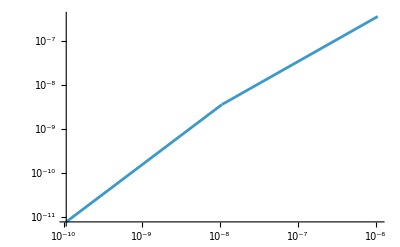

```mathematica
LogLogPlot[press[rho],{rho,(1/100)*rhostar,100*rhostar}]
```

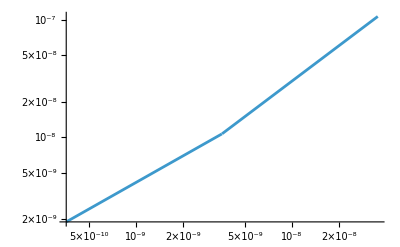

```mathematica
LogLogPlot[rhoofp[p],{p,(1/10)*pstar,10*pstar}]
```

```mathematica
(*2. Initial Conditions from Series Expansions*)

(*The T-O-V equations are singular at r=0. To start our numerical integration at a 
small radius r > 0, we need initial values for mass m(r) and pressure p(r). These 
are derived from a power series expansion near the origin, as described in Schutz, 
Exercise 10.15.*)
(*We create a function `getInitialConditions` that takes a central density `rhoc` 
and calculates the appropriate starting values at a small radius `rmax`.*)
maxRelativeErrorAcceptable = 0.001;
(* ::Code:: *)
speedofsound[rho_]:= Sqrt[adiabaticIndex[rho]*press[rho]/rho];
getPowerSeriesCoeffs[rhoc_] := Module[
    {pc, p2, rho2, m3,m5,  m, rho},
  (* Central pressure from EOS *)
  pc = press[rhoc];
  (* Second derivative of pressure at the center (from Scott, eqn. 10.43) *)
  p2 = N[-(2/3)*Pi*(rhoc + pc)*(rhoc + 3*pc)];
  (* Second derivative of density at the center (from Scott, eqn. 10.43) *)
  rho2 = p2*rhoc/(adiabaticIndex[rhoc]*pc);

  (* Calculate m(r) and rho(r) at this small radius using the series *)
  (* See Scott eqn(10.42) in the solution to Exer. 10.15: *)
  m3 = (4/3)*Pi*rhoc;
  m5 = (4/5)*Pi*rho2;
  m = m3*r^3 + m5*r^5;
  rho = rhoc + rho2*r^2;
  
  (* Return the list {starting radius, mass, pressure} *)
  {pc, p2, rho2, m3, m5}
]
getICr[rhoc_] := Module[
    {coeffs,pc, p2, rho2, m3,m5,rmaxmass,rmaxpress, rmaxrho, r, m, rho, p},
  (* Central pressure from EOS *)
  coeffs = getPowerSeriesCoeffs[rhoc];
  (* Second derivative of pressure at the center (from Scott, eqn. 10.43) *)
  pc = coeffs[[1]];
  p2 = coeffs[[2]];
  rho2 = coeffs[[3]];
  m3 = coeffs[[4]];
  m5 = coeffs[[5]];
  (* Estimate a small radius 'rmax' where the series is still accurate *)
  rmaxmass =  Sqrt[Abs[Sqrt[maxRelativeErrorAcceptable]*m3/m5]];
  rmaxpress = Sqrt[Abs[Sqrt[maxRelativeErrorAcceptable]*pc/p2]];
  rmaxrho = Sqrt[Abs[Sqrt[maxRelativeErrorAcceptable]*rhoc/rho2]];
  r = Min[rmaxpress, rmaxrho,rmaxmass];
  {r,rmaxmass,rmaxpress,rmaxrho}
    ]
```

```mathematica
csstar=N[speedofsound[rhostar]]
coefflist=getPowerSeriesCoeffs[rhostar]
rmaxs = getICr[rhostar]
getInitialConditions[rhoc_]:=Module[
    {rmaxs,rstart,coefflist,pc,p2,rho2,m3,m5,mstart,pstart,rhostart},
    rmaxs = getICr[rhoc];
    rstart = rmaxs[[1]];
    coefflist=getPowerSeriesCoeffs[rhoc];
    pc = coefflist[[1]];
    p2 = coefflist[[2]];
    rho2 = coefflist[[3]];
    m3 = coefflist[[4]];
    m5 = coefflist[[5]];
    mstart = m3*rstart^3+m5*rstart^5;
    pstart = pc + p2*rstart^2;
    rhostart = rhoc + rho2*rstart^2;
    {rstart,mstart,pstart,rhostart}
]
getInitialConditions[rhostar]
```

0.333333

{3.56315×10^-9,-6.38171×10^-16,-5.74354×10^-15,4.47758×10^-8,-1.44351×10^-14}

{242.598,313.193,420.192,242.598}

{242.598,0.627173,3.52559×10^-9,1.03514×10^-8}

```mathematica
(* Try just one step *)
rStop=200000;
rhoc = 1.1 * rhostar;
Print["\n for rhoc = ", rhoc];
  (* Get initial conditions {r_start, m_start, p_start} *)
initialConditions = getInitialConditions[rhoc];
rStart = initialConditions[[1]];
mStart = initialConditions[[2]];
pStart = initialConditions[[3]];
rhoStart = initialConditions[[4]];
Print["\n found  these starting values "];
Print["r start = ", rStart];
Print["m start = ", mStart];
Print["p start = ", pStart]; 
Print["rho start = ", rhoStart]; 
Print["diff: p start - press(rho start)",pStart-press[rhoStart]]
Print["this is so small it makes no difference to the solution"]
```

for rhoc = 1.17584×10^-8

found  these starting values

r start = 231.308

m start = 0.597986

p start = 3.87815×10^-9

rho start = 1.13865×10^-8

diff: p start - press(rho start)8.26295×10^-11

this is so small it makes no difference to the solution

```mathematica
eqnsys = {
   m'[r] == 4*Pi*r^2*rhoofp[p[r]],
   p'[r] == -(rhoofp[p[r]] + p[r])*(m[r] + 4*Pi*r^3*p[r]) / (r*(r - 2*m[r]))
   }

{msol,psol,mpsol,ppsol} = NDSolveValue[
    {eqnsys[[1]], eqnsys[[2]], m[rStart] == mStart, p[rStart] == pStart},
    {m, p,m',p'},
    {r, rStart, rStop}, (* Integrate out to a large radius *)
    Method->{"ExplicitRungeKutta","DifferenceOrder"->8},InterpolationOrder->All
    ];
(* Alternatively, we could take the pressure from the EOS and the starting
density, rhoc *)
{msolalt,psolalt} = NDSolveValue[
    {eqnsys[[1]], eqnsys[[2]], m[rStart] == mStart, p[rStart] == N[press[rhoStart]]},
    {m, p},
    {r, rStart, rStop}, (* Integrate out to a large radius *)
    Method->{"ExplicitRungeKutta","DifferenceOrder"->8},InterpolationOrder->All
    ];
(* Alternatively, we could use the default Method! *)    
{msolbis,psolbis} = NDSolveValue[
    {eqnsys[[1]], eqnsys[[2]], m[rStart] == mStart, p[rStart] == N[press[rhoStart]]},
    {m, p},
    {r, rStart, rStop}, (* Integrate out to a large radius *)
    Method->Automatic
    ];
```

{m'[r]==4 π r^2 If[3.56315×10^-9≤p[r],3 p[r],(Max[0,p[r]]/kGU)^(3/4)],p'[r]==1/(r (r-2 m[r]))(-If[3.56315×10^-9≤p[r],3 p[r],(Max[0,p[r]]/kGU)^(3/4)]-p[r]) (m[r]+4 π r^3 p[r])}

In case you forgot, we have  = 1 neucleon(s) per electron

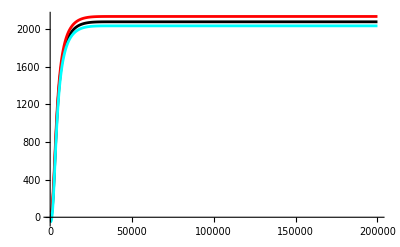

```mathematica
Print["\n In case you forgot, we have  = ", μ, " neucleon(s) per electron"];
Plot[{msol[r],msolalt[r]+50,msolbis[r]-50},{r,rStart,rStop},PlotRange->All,PlotStyle->{Black,Red,Cyan}]
```

Pressure is interesting, but not helpful for finding R

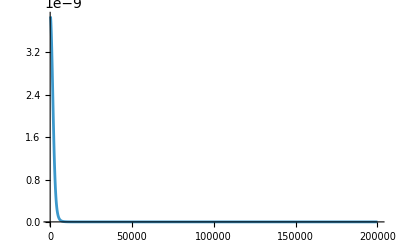

```mathematica
Print["\n Pressure is interesting, but not helpful for finding R "]
Plot[psol[r],{r,rStart,rStop},PlotRange->All]
```

Pressure gradient is interesting, but not helpful for finding R

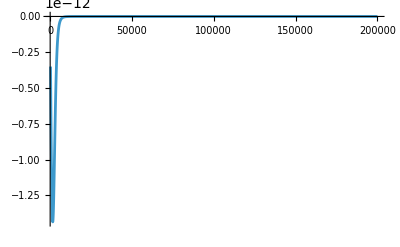

```mathematica
Print["\n Pressure gradient is interesting, but not helpful for finding R "]
Plot[ppsol[r],{r,rStart,rStop},PlotRange->All]
```

Bingo! Log Pressure is very helpful for finding R !!!

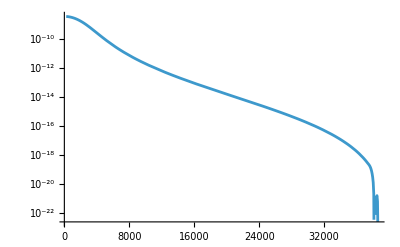

```mathematica
Print["\n Bingo! Log Pressure is very helpful for finding R !!! "]
LogPlot[psol[r],{r,rStart,rStop},PlotRange->All]
```

```mathematica
(*3. Numerical Integration of the T-O-V Equations*)

(*Now we solve the coupled differential equations for stellar structure: the 
mass-continuity equation and the Tolman-Oppenheimer-Volkoff (T-O-V) equation 
for hydrostatic equilibrium.*)

(*Defining the Differential Equations*)

(*The system of equations is (from Schutz, Chapter 10):*)
(*dm/dr = 4πr^2 ρ(p)*)
(*dp/dr = -(ρ(p) + p)(m + 4πr^3 p) / (r(r-2m))*)

(* Define the differential equations. Note that rho is a function of p. *)
eqns = {
   m'[r] == 4*Pi*r^2*rhoofp[p[r]],
   p'[r] == -(rhoofp[p[r]] + p[r])*(m[r] + 4*Pi*r^3*p[r]) / (r*(r - 2*m[r]))
   }

(*Solving for Different Central Densities*)
Print["\n Solving ODE from ICs from the power series with a max relative error:"];
Print[maxRelativeErrorAcceptable]
(*We will now solve the system for each of the central densities requested in 
the exercise. For each case, we first get the initial conditions at a small 
radius `r_start`, and then use `NDSolve` to integrate outwards until the 
pressure drops to zero, which defines the star's surface.*)

(* List of central densities to model (as multiples of rhostar) *)
rhocRatios = {0.1, 0.8, 1.2, 2, 5, 10, 100,1000};

(* We will store the solutions (InterpolatingFunction objects) in a list *)
solutions = {};
rStartAll = {};
(* Loop through each central density ratio *)
For[i = 1, i <= Length[rhocRatios], i++,
  rhoc = rhocRatios[[i]] * rhostar;
  Print["\n for rhoc = ", rhoc];
  (* Get initial conditions {r_start, m_start, p_start} *)
  initialConditions = getInitialConditions[rhoc];
  rStart = initialConditions[[1]];
  mStart = initialConditions[[2]];
  pStart = initialConditions[[3]];
  Print["\n found  these starting values "];
  Print["r start = ", rStart];
  Print["m start = ", mStart];
  Print["p start = ", pStart]; 
  (* Numerically solve the ODEs *)
  (* We use "WhenEvent" to stop the integration when p[r] hits zero *)
  sol = NDSolveValue[
    {eqns[[1]], eqns[[2]], m[rStart] == mStart, p[rStart] == pStart},
    {m, p},
    {r, rStart, rStop} (* Integrate out to a large radius *)
    ];
  (* Method -> "StiffnessSwitching", *)
  (* "WhenEvent"[p[r] < 1*^-20, "StopIntegration"] *)
  AppendTo[solutions, sol];
  AppendTo[rStartAll, rStart];
    ];
```

{m'[r]==4 π r^2 If[3.56315×10^-9≤p[r],3 p[r],(Max[0,p[r]]/kGU)^(3/4)],p'[r]==1/(r (r-2 m[r]))(-If[3.56315×10^-9≤p[r],3 p[r],(Max[0,p[r]]/kGU)^(3/4)]-p[r]) (m[r]+4 π r^3 p[r])}

Solving ODE from ICs from the power series with a max relative error:

0.001

for rhoc = 1.06894×10^-9

found  these starting values

r start = 1136.93

m start = 6.48664

p start = 1.60157×10^-10

for rhoc = 8.55155×10^-9

found  these starting values

r start = 465.162

m start = 3.55403

p start = 2.56251×10^-9

for rhoc = 1.28273×10^-8

found  these starting values

r start = 221.461

m start = 0.572528

p start = 4.2307×10^-9

for rhoc = 2.13789×10^-8

found  these starting values

r start = 171.543

m start = 0.443478

p start = 7.05117×10^-9

for rhoc = 5.34472×10^-8

found  these starting values

r start = 108.493

m start = 0.28048

p start = 1.76279×10^-8

for rhoc = 1.06894×10^-7

found  these starting values

r start = 76.7163

m start = 0.198329

p start = 3.52559×10^-8

for rhoc = 1.06894×10^-6

found  these starting values

r start = 24.2598

m start = 0.0627173

p start = 3.52559×10^-7

for rhoc = 0.0000106894

found  these starting values

r start = 7.67163

m start = 0.0198329

p start = 3.52559×10^-6

```mathematica
(*4. Analysis and Plotting of Results*)


(*With the solutions for each model, we can now extract the stellar properties
 (like total mass M and radius R) and plot the results as requested in the 
 textbook.*)

(*Extracting Mass and Radius*)

(* Extract the mass and pressure functions from the solutions *)
massFunctions = solutions[[All, 1]];
pressureFunctions = solutions[[All, 2]];

(* Find the radius R and total mass M for each star *)
(* The radius is the upper bound of the domain of the pressure function *)
(* 
Unfortunately, the two lines below did not work:
radii = Table[pressureFunctions[[i]]["Domain"][[1, 2]], {i, 1, Length[solutions]}];
masses = Table[massFunctions[[i]][radii[[i]]], {i, 1, Length[solutions]}];

But below we have a nice example of how to display the results !

(* Display the results in a table *)
resultsTable = Table[
  {"ρc/ρ*" -> rhocRatios[[i]], 
   "Radius R (m)" -> Round[radii[[i]]], 
   "Mass M (m)" -> Round[masses[[i]], 0.1],
   "M/R" -> Round[masses[[i]]/radii[[i]], 0.001]},
  {i, 1, Length[solutions]}
];

Grid[Prepend[resultsTable, {"Model", "Radius R (m)", "Mass M (m)", "M/R"}], Frame -> All]

*)

(*Plotting Pressure vs. Radius*)

(*This plot shows how the pressure p(r) drops from its central value to zero at
 the surface for each model.*)
```

200000

76.7163

0.198329

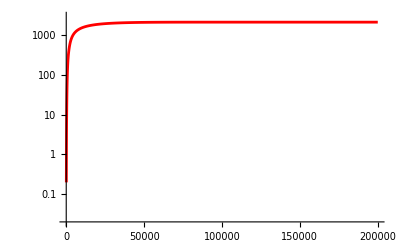

```mathematica
rRight=rStop
rLeft=10;
mBottom=0.02;
mTop = 3000;
rStartAll[[6]]
massFunctions[[6]][rStartAll[[6]]]
LogPlot[massFunctions[[6]][r],{r,rStartAll[[6]],rRight},PlotStyle -> Red,PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}]
```

Just in case you still cannot remember 1 protons and neutrons per 
little negative guy

200000

50

0.1

5000

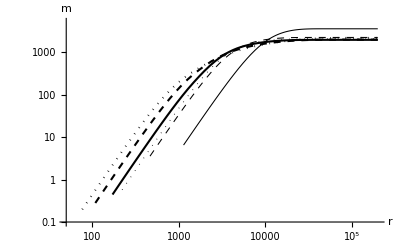

```mathematica
(* Loop through each central density ratio, look at plotts*)
Print["Just in case you still cannot remember ", μ, " protons and neutrons per 
little negative guy"]
rRight=rStop
rLeft=50 (* 10 ; 50 *)
mBottom=0.1 (*0.01 ;  2 *)
mTop = 5000
subplot1=LogLogPlot[massFunctions[[1]][r],{r,rStartAll[[1]],rRight},
         PlotStyle -> Directive[Black,Solid,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot2=LogLogPlot[massFunctions[[2]][r],{r,rStartAll[[2]],rRight},
         PlotStyle -> Directive[Black,Dashed,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot3=LogLogPlot[massFunctions[[3]][r],{r,rStartAll[[3]],rRight},
         PlotStyle -> Directive[Black,Dotted,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot4=LogLogPlot[massFunctions[[4]][r],{r,rStartAll[[4]],rRight},
         PlotStyle -> Directive[Black,Solid,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot5=LogLogPlot[massFunctions[[5]][r],{r,rStartAll[[5]],rRight},
         PlotStyle -> Directive[Black,Dashed,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot6=LogLogPlot[massFunctions[[6]][r],{r,rStartAll[[6]],rRight},
         PlotStyle -> Directive[Black,Dotted,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
Show[subplot1,subplot2,subplot3,subplot4,subplot5,subplot6,
 AxesLabel -> {"r", "m"},
 AxesStyle -> Directive[Black,FontFamily -> "Times", Italic, 18],
 TicksStyle->Directive[Black,FontFamily->"Helvetica",FontSlant->"Plain",FontSize->14]]
```

That's right 1 protons and neutrons per 
little negative guy

200000

50

1800

3600

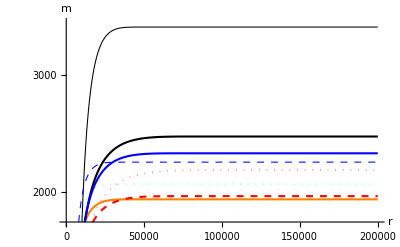

```mathematica
(* Plots to read the mass: added two extremes to check sequence*)
Print["That's right ", μ, " protons and neutrons per 
little negative guy"]
rRight=rStop
rLeft=50 (* 10 ; 50 *)
mBottom=1800 (*0.01 ;  2 *)
mTop =  3600 (* 900 *)
subplot1=LogPlot[massFunctions[[1]][r],{r,rStartAll[[1]],rRight},
         PlotStyle -> Directive[Black,Solid,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot2=LogPlot[massFunctions[[2]][r],{r,rStartAll[[2]],rRight},
         PlotStyle -> Directive[Blue,Dashed,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot3=LogPlot[massFunctions[[3]][r],{r,rStartAll[[3]],rRight},
         PlotStyle -> Directive[Cyan,Dotted,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot4=LogPlot[massFunctions[[4]][r],{r,rStartAll[[4]],rRight},
         PlotStyle -> Directive[Orange,Solid,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot5=LogPlot[massFunctions[[5]][r],{r,rStartAll[[5]],rRight},
         PlotStyle -> Directive[Red,Dashed,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot6=LogPlot[massFunctions[[6]][r],{r,rStartAll[[6]],rRight},
         PlotStyle -> Directive[Pink,Dotted,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot7=LogPlot[massFunctions[[7]][r],{r,rStartAll[[7]],rRight},
         PlotStyle -> Directive[Black,Solid,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot8=LogPlot[massFunctions[[8]][r],{r,rStartAll[[8]],rRight},
         PlotStyle -> Directive[Blue,Solid,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
Show[subplot1,subplot2,subplot3,subplot4,subplot5,subplot6,subplot7,subplot8,
 AxesLabel -> {"r", "m"},
 AxesStyle -> Directive[Black,FontFamily -> "Times", Italic, 18],
 TicksStyle->Directive[Black,FontFamily->"Helvetica",FontSlant->"Plain",FontSize->14]]
```

```mathematica
rRight=110000  (*rStop, 30 000  *)
rLeft=0 (* 10 ; 50 *)
mBottom=10^(-25) (*0.1 ;  2 *)
mTop = 10^(-6)
subplot1=LogPlot[pressureFunctions[[1]][r],{r,rStartAll[[1]],rRight},
         PlotStyle -> Directive[Black,Solid,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot2=LogPlot[pressureFunctions[[2]][r],{r,rStartAll[[2]],rRight},
         PlotStyle -> Directive[Black,Dashed,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot3=LogPlot[pressureFunctions[[3]][r],{r,rStartAll[[3]],rRight},
         PlotStyle -> Directive[Black,Dotted,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot4=LogPlot[pressureFunctions[[4]][r],{r,rStartAll[[4]],rRight},
         PlotStyle -> Directive[Black,Solid,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot5=LogPlot[pressureFunctions[[5]][r],{r,rStartAll[[5]],rRight},
         PlotStyle -> Directive[Black,Dashed,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot6=LogPlot[pressureFunctions[[6]][r],{r,rStartAll[[6]],rRight},
         PlotStyle -> Directive[Black,Dotted,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
Show[subplot1,subplot2,subplot3,subplot4,subplot5,subplot6,
 AxesLabel -> {"r", "p"},
 AxesStyle -> Directive[Black,FontFamily -> "Times", Italic, 18],
TicksStyle->Directive[Black,FontFamily->"Helvetica",FontSlant->"Plain",FontSize->14]
  ]
```

110000

0

1/10000000000000000000000000

1/1000000

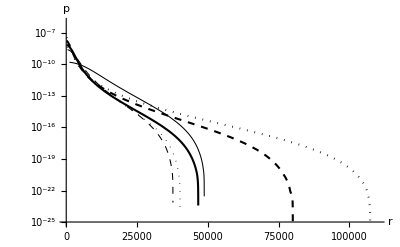

-Graphics-

110000

0

1/10000000000000000000000000

1/1000000

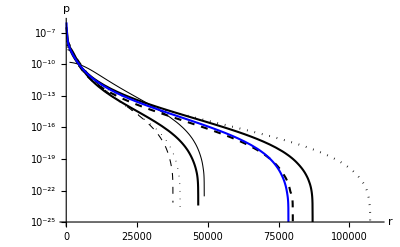

```mathematica
rRight=110000  (*rStop, 30 000  *)
rLeft=0 (* 10 ; 50 *)
mBottom=10^(-25) (*0.1 ;  2 *)
mTop = 10^(-6)
subplot1=LogPlot[pressureFunctions[[1]][r],{r,rStartAll[[1]],rRight},
         PlotStyle -> Directive[Black,Solid,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot2=LogPlot[pressureFunctions[[2]][r],{r,rStartAll[[2]],rRight},
         PlotStyle -> Directive[Black,Dashed,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot3=LogPlot[pressureFunctions[[3]][r],{r,rStartAll[[3]],rRight},
         PlotStyle -> Directive[Black,Dotted,AbsoluteThickness[0.75]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot4=LogPlot[pressureFunctions[[4]][r],{r,rStartAll[[4]],rRight},
         PlotStyle -> Directive[Black,Solid,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot5=LogPlot[pressureFunctions[[5]][r],{r,rStartAll[[5]],rRight},
         PlotStyle -> Directive[Black,Dashed,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot6=LogPlot[pressureFunctions[[6]][r],{r,rStartAll[[6]],rRight},
         PlotStyle -> Directive[Black,Dotted,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot7=LogPlot[pressureFunctions[[7]][r],{r,rStartAll[[7]],rRight},
         PlotStyle -> Directive[Black,Solid,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];
subplot8=LogPlot[pressureFunctions[[8]][r],{r,rStartAll[[8]],rRight},
         PlotStyle -> Directive[Blue,Solid,AbsoluteThickness[1.5]],PlotRange -> {{rLeft, rRight}, {mBottom, mTop}}];

Show[subplot1,subplot2,subplot3,subplot4,subplot5,subplot6,subplot7,subplot8,
 AxesLabel -> {"r", "p"},
 AxesStyle -> Directive[Black,FontFamily -> "Times", Italic, 18],
TicksStyle->Directive[Black,FontFamily->"Helvetica",FontSlant->"Plain",FontSize->14]
  ]
```

## Chapter 12: Gravitational wave astronomy

## Exercise 12.1

### Use Eq. 12.2 to find the final gravitation wave frequencies at merger of pairs of equal-mass black holes of masses 10, million and billion solar masses, respectively.

```mathematica
(* The problem provides the key formula, which is also derived and discussed in
 Section 12.2 of the textbook.
The formula is given as: 
ffinal = 4.0 / Mchirp
where ffinal is the final frequency in kHz and Mchirp is the "chirp mass" of 
the system in units of solar masses. *)

(*First, define a Mathematica function based on Equation (12.2) from the 
textbook to easily calculate the final frequency for any given chirp mass.*)

ffinal[Mchirp_] := 4.0 / Mchirp

(* The formula for the chirp mass is given in Chapter 9, Equation (9.151):*)
(*Mchirp = (m1*m2)^(3/5) / (m1+m2)^(1/5)
where m1 and m2 are the component masses of the binary system, m1 >= m2 by 
convention. *)

(* Second, define a Mathematica function to calculate the chirp mass *)
chirpMass[m1_, m2_] := (m1 * m2)^(3/5) / (m1 + m2)^(1/5)

(* Calculate the chirp mass for the 3 binary systems: *)  

(* S1: m1 = m2 = 10 solar masses *)

mChirpS1 = chirpMass[10, 10]
N[mChirpS1]
```

```mathematica
(* Finally frequency in kHz *)
freqS1 = ffinal[mChirpS1]
```

```mathematica
(* S2: m1 = m2 = 10^6 solar masses *)
mChirpS2 = chirpMass[10^6, 10^6]
(* Finally frequency in kHz *)
freqS2 = ffinal[mChirpS2]
```

```mathematica
(* S3: m1 = m2 = 10^9 solar masses *)
mChirpS3 = chirpMass[10^9, 10^9]
(* Finally frequency in kHz *)
freqS3 = ffinal[mChirpS3]
```

## Exercise 12.7 (f)

### Here we explore solving Eq.(12.26) for the inclination angle iota.

#### (f) This result shows that iota needs to get fairly large before epsilon becomes measurable, or equivalently the ratio r becomes measurably different from 1. Suppose that r is measured to be 1, with an error of 1%. Show that iota might be as large as 0.53 radians or 30°.

```mathematica
(*Exercise 12.7(f) asks us to explore the uncertainty in measuring the 
inclination angle, ι, of a nearly face-on binary system. 
Specifically, it states:
"Suppose that r is measured to be 1, with an error of 1%. Show that ι might 
be as large as 0.53 radians, or 30°."*)
(*Here, `r` is the ratio of the measured polarization amplitudes, |h+|/|h×|, 
and ι is the inclination angle of the binary's orbit (where ι = 0 is a 
face-on orbit).*)
(*The problem states that `r` is measured to be 1 with an error of 1%. We have constructed
r >= 1 so this means the likely measured value could be up to 1.01 *)
(* We could simply apply the arccos function to Scott eqn(12.37):
z = r - sqrt(r^2 - 1) = cos(ι)
ι = arccos(z)
*)
inclinationAngle[r_] :=ArcCos[r-Sqrt[r^2-1]]
iotaDirect=inclinationAngle[1.01]
```

The above is the inclination in radians. Below we convert to degrees.

```mathematica
(* The above result is the maximum likely inclination angle in radians. In degrees: *)
iotaDirect*180/Pi
```

The above result is approximately 30°, confirming the problem statement.

The above is a legitimate solution, but does not follow the spirit of the exercise. The Exercise 12.7(f) builds directly on the results from the previous parts of Exercise 12.7, in which explore the relationship between the measured amplitude ratio `r` and the inclination `ι` (Greek letter iota). A key relationship for this part comes from the approximation derived in Exercise 12.7(e) for nearly face-on systems (where `r` is close to 1 and `ι` is small). In Exercise 12.7(d) we defined variable, ϵ, as the deviation of the measured 
amplitude ratio from 1:
ϵ = r - 1
Then in Exercise 12.7(e) we showed that for small ι, this is related to the inclination by:
ϵ ≈ ι^4 / 8
(See tip in Exercise 12.11(d) for entering Greek letters.)
As stated above, the problem gives that `r` is measured to be 1 with an error of 1%.
 We have constructed r >= 1 so this means the likely measured value could be up to 
 1.01 and the maximum  likely value for ϵ is 0.01.

```mathematica
Clear[ι]   (* This is how we clear a previously defined variable *)
```

```mathematica
(*
We can now set up an equation in Mathematica to solve for the inclination 
angle ι that corresponds to this maximum error using the result of Exer 12.7(e).*)

(* The maximum deviation from r=1 is 1%, or 0.01 *)
epsilon = 0.01;

(* The relationship from Exercise 12.7(e) *)
equation = epsilon == ι^4 / 8;

(* Of course we could invert this relation to find ι , but as a demonstration
of Mathematica, let's use its Solve function. This remindes us that we must be
explicit about wanting a real (and not complex) answer. Since ι must be a real, 
positive angle, we will select the appropriate solution as indicated below *)

(* Solve the equation for ι over the real numbers *)
solutions = Solve[equation, ι, Reals]
```

```mathematica
(*The positive solution is the physically meaningful one for the inclination angle.*)

(* Here is how we could extract the positive solution for ι in radians *)
iotaInRadians = ι /. solutions[[2]]

(*This matches the value of 0.53 radians given in the problem statement. Now, let's convert this to degrees to confirm the second part of the question.*)
```

The above is the inclination in radians. Below we convert to degrees.

```mathematica
(* Convert the result from radians to degrees *)
iotaInDegrees = iotaInRadians * (180 / Pi)
```

The above result is approximately 30°, again confirming the problem statement.

## Exercise 12.7(g)

#### Show that the percentage change of 1 + cos^2(ι) in this range is about 7%. This will be the uncertainty in the inferred distance for a face-on signal, even though the amplitudes themselves are measured to 1% accuracy.

This part investigates how the uncertainty in the inclination angle (found in part f) affects the inferred amplitude of the gravitational wave, and therefore the inferred distance.

From Chapter 9, Schutz Eq. (9.100), the amplitude of the h+ polarization is proportional to the factor (1 + Cos[ι]^2). We need to calculate how much this factor changes as inclination varies from iota = 0 (perfectly face-on) to the maximum value of iota = 0.531829 radians that we found in Exer. 12.7(f).

```mathematica
(* Define a function for the amplitude factor *)
amplitudeFactor[ι_] := 1 + Cos[ι]^2
```

Now we apply this function at the two extreme values of inclination:

```mathematica
(* Calculate the factor for a perfectly face-on system (iota = 0) *)
factorFaceOn = amplitudeFactor[0]

(* Calculate the factor at the maximum possible inclination from part (f) *)
factorMaxIota = amplitudeFactor[0.5318295896944989]
(* Calculate the factor at the midway inclination from part (f) *)
factorMidwayIota = amplitudeFactor[0.5318295896944989/2]
```

Now we calculate the percentage change between these two values. The percentage change is the absolute difference divided by the mid-point value (midway between face-on and maximum likely inclination), multiplied by 100 to convert to percent:

```mathematica
percentageChange = Abs[factorMaxIota - factorFaceOn] / factorMidwayIota * 100
```

The result is approximately 13.3%, which is almost twice the value of “about 7%” stated in the problem. A likely explanation is that the 7% uncertainty is about the midway value, so we can justify dividing by two:

```mathematica
percentageChange/2
```

Rounding off, we confirm an uncertainty of about 7% about the midway inclination.

Discussion 

This pair of exercises provides a crucial insight into the challenges of gravitational wave astronomy. As discussed in Section 12.3 of the textbook, the inclination angle is a key parameter needed to accurately determine the distance to a standard siren.

Our calculations show that for nearly face-on systems (which produce the strongest and most easily detectable signals), even a small 1% uncertainty in the measured polarization amplitudes leads to a very large uncertainty in the inclination angle (up to 30°).

Furthermore, this large uncertainty in iota propagates into a significant uncertainty (about 7%) in the inferred amplitude of the wave. Since the inferred distance is inversely proportional to the measured amplitude, this translates directly into a ~7% uncertainty in the distance measurement. This makes it difficult to get a precise measurement of cosmological parameters like the Hubble-LemaΙtre constant from a single, nearly face-on event.

## Exercise 12.9

### Here we examine how an optimum all-sky search might correct for signal modulation and pulsar spin-down, and we use that to do a rough estimation of the number of arithmetic operations that would be required to search for a gravitational wave pulsar in six months of data. Each arithmetic operation is called, in the language of computing, a floating-point operation. For the purposes of this calculation we assume that the search goes up to 2 kHz in gravitational wave frequency, because theoretically it would be possible for a neutron star to spin at 1 kHz. We assume that the data are sampled at 4 kHz, which is the minimum sampling rate to allow a 2 kHz bandwidth search. The method will be to demodulate the recorded data for a particular patch on the sky, as described in the text, then to compensate for a particular spin-down value by the method described below, and then to do a Fourier transform for each combination of sky patch and spin-down value, in order to find a signal. Since this is a rough estimate, we regularly round our results to one significant figure. It should be emphasized that there can be other approaches to this problem that are more efficient, but not by huge factors. The approach here is straightforward to describe and shows rather readily that an optimum search is far out of reach.

#### (a) Show that if the duration of the observation is s, the number of data samples is , and the frequency resolution of the observation is

```mathematica
(*Part (a): Number of Data Samples*)

(*The problem asks for Ns, the number of samples in a data stream of 
duration T = 0.15e8 seconds (about one half year) with a sampling rate of 
4000 Hz.*)

(* Duration of the observation in seconds, Tobs *)
Tobs = 0.15*10^8;
(* Sampling rate in Hz *)
samplingRate = 4000;
(* Number of samples Ns *)
Ns = Tobs * samplingRate
```

```mathematica
(* For the sake of curiousity, here is a much more precise calculation *)
secperyear = 365.2425 * 24 * 3600;
Nsprecise = 0.4*^4 * secperyear * (1/2)
```

The frequency resolution is calculated from the reciprocal of the longest period that is resolved, which here is 6 months. Schutz is more conservative and  assumes half this resolution.

```mathematica
(* Frequency resolution, Delta f in Hz*)
Deltaf = 1/Tobs
```

#### (b) ... Assuming that the interpolation requires of order ten operations per data point, show that each demodulation requires operations.There is, of course, one demodulation for each resolvable patch on the sky.

```mathematica
(* Number of operations to demodulate the Doppler shift for data from a given patch
of the sky, Ndemod *)
Ndemod = 10*Ns
```

#### (c) To correct for the pulsar’s changing signal frequency, we will assume that the only parameter we need is the first time-derivative of the frequency, i.e. that the frequency changes linearly in time over the observation period. We shall handle this in the same way as the demodulation, by shifting to a different time measure. We assume that the source’s wavefronts are emitted at a uniform rate with respect to a clock that is slowing down. Once we map that clock’s time onto barycenter time, we restore the pulsar to a single-frequency signal and we can use a Fourier transform to search for it. Letting represent the start of the observation time in the barycenter, we can give concrete expression to this by relating the pulsar’s `clock’ to barycentric time t as follows: where is a parameter known as the slowdown time, a measure of how long it takes the pulsar to change its frequency by a significant amount. Since realistic slowdown times are larger than years, we always have , so that the fractional changes in clock rates are small.

```mathematica
(*Part (c): Computational Cost Estimation*)

(*This part is broken into several steps to build up the final estimate of 
the total computational cost.*)

(* Define constants from the problem *)
Tobs = 0.15*^8; (* Observation time for this part (6 months) *)
f0 = 2000; (* Maximum frequency to search in Hz *)
Deltaf = 1.3*^-7; (* Frequency resolution from a 6-month observation *)
numSkyPatches = 0.3*^13; (* Number of independent sky patches to search *)
```

```mathematica
(*Sub-part (iii): Maximum Spin-Down*)
(*We need to find the maximum inverse spin-down time, (1/τ)_max, for a 
pulsar that slows from 2000 Hz to 1000 Hz in 1000 years.*)

fInitial = 2000; (* Hz *)
fFinal = 1000; (* Hz *)
timeToSlow = 1000 * secperyear; (* seconds *)
```

```mathematica
(* The rate of change of frequency is df/dt = (fFinal - fInitial)/timeToSlow *)
dfdt = (fFinal - fInitial) / timeToSlow;
(* From the text, df/dt = -2*f0/τ. We solve for 1/τ. *)
invTauMax = Abs[dfdt / (2*f0)]
(* Compare with Scott eqn.(12.70)*)
```

```mathematica
(*Sub-part (iv): Spin-Down Resolution*)
(*Next, we find the resolution with which we can measure the spin-down 
parameter, Δ(1/τ).*)

deltaInvTau = Deltaf / (2 * Tobs * f0)

(* Compare with Scott eqn.(12.72) for the conservative resolution of Schutz. 
Compare with Scott eqn.(12.73) for the standard resolution.*)
```

```mathematica
(*Sub-part (vi): Number of Independent Searches*)
(*The total number of searches is the number of sky patches multiplied by the 
number of spin-down templates  we need to check. 
The number of spin-down templates, n in Scott eqn(12.75), is the total range 
of spin-down values divided by the resolution.*)

numSpinDownTemplates = invTauMax / deltaInvTau  (* compare with Scott eqn(12.75)*)
numberSearches = numSkyPatches * numSpinDownTemplates (* compare with Scott eqn(12.76)*)
```

```mathematica
(*Sub-part (vii): Flops per Search*)
(*The exercise provides a formula for the number of floating-point operations 
per search.*)
(* We need the natural lorgarithm of the number of the number of samples Ns *)
N[Log[Nsprecise],6]
(* We use the Nsprecise value from part (a) *)
flopsPerSearch = (Log[Nsprecise] + 10 + 10) * Nsprecise (* Compare with Scott eqn.(12.77) *)
```

```mathematica
(*Sub-part (viii): Total Computing Resources*)
(*Finally, we calculate the total flops required for the entire search over six
 months and determine how many 400 petaflop supercomputers would be needed to 
 complete it in time.*)

(* Total flops needed for the search *)
flopsEverySixMonths = flopsPerSearch * numberSearches (* Scott eqn(12.78)*)
```

```mathematica
(* Convert this to a rate in flops per second *)
secondsInSixMonths = 0.5 * secperyear;
flopsPreciseRate = flopsEverySixMonths / secondsInSixMonths
(* Scott eqn.(12.79)*)
```

```mathematica
(* Define the speed of one supercomputer in flops/sec *)
petaflop = 10^15;
supercomputerSpeed = 400 * petaflop;

(* Calculate the number of machines required *)
numMachines = flopsPreciseRate / supercomputerSpeed
```

Conclusion for Exercise 12.9
Even correcting the factor of ten thousand exaggeration of the question, the final result is still staggering. To perform an optimal, all-sky search for a single unknown pulsar in six months of data would require nearly 5 million (and not 50 billion) of the world’s fastest supercomputers.
This calculation powerfully illustrates why such “blind” searches are computationally impossible to perform optimally. Instead, researchers must use hierarchical methods and other clever algorithms to conduct sub-optimal searches, which trade some sensitivity for a computationally feasible problem. It also highlights the importance of targeted searches, where the sky position and frequency are already known from radio pulsar observations, dramatically reducing the number of required templates.

## Exercise 12.11(d)

### (d) In Schutz’s Table 12.1, look at the masses given for GW170817. The collaboration published uncertainty ranges for these values as well (abbott2019properties). The uncertainty in the chirp mass was one part in , so for the purposes of this exercise, we take it as exactly known. The 90% uncertainty range of the total mass was asymmetrical, given as . Calculate the corresponding 90% bounds on the component masses and . (These are only approximate bounds; a full analysis would take into account the uncertainty in the chirp mass and its correlation with the uncertainty in the total mass.).

```mathematica
(*From Table 12.1 in the textbook, we have the best-fit masses for the two 
neutron stars in GW170817.*)

m1 = 1.44; (* Mass of the primary component in solar masses *)
m2 = 1.28; (* Mass of the secondary component in solar masses *)

(*From these, we can calculate the total mass (M) and the reduced mass (μ).*)

M = m1 + m2            (* Scott eqn.(12.100) *)
μ = (m1 * m2) / M      (* Scott eqn.(12.101) *)
```

Tip: 
To get the Greek letter mu above we have several options
1) use the syntax :
	\[x] 
and replace “x” with the name of the Greek letter in capital letters, e.g. replace “x” with “Mu” gives a lowercase mu, μ.
2) use keyboard shortcuts:
	esc m esc
gives μ.
For ψ type:
	esc psi esc
3) Using palettes. Select Insert from the Default toolbar at the top of the page. (Make sure the Default toolbar appears at the top with “Evaluation” at the top left, and Insert at the top right. If not, from the main menu, Window, Toolbar, select Default.)

```mathematica
(*The formulas from part (b) of the exercise give the rate of change of the 
component masses with respect to a change in the total mass.*)

dm1dM = 1/2 + (1/2 - μ/(3*M)) / Sqrt[1 - 4*μ/M];
dm2dM = 1/2 - (1/2 - μ/(3*M)) / Sqrt[1 - 4*μ/M];


(*Calculating the Uncertainty Bounds*)

(*The problem gives the asymmetric 90% confidence interval for the total mass.*)

deltaMUpper = 0.04; (* Upper uncertainty bound for M *)
deltaMLower = -0.01; (* Lower uncertainty bound for M *)

(*We can now calculate the corresponding uncertainties for m1 and m2 by 
multiplying the derivatives by these δM values.*)

(* Uncertainty for m1 *)
deltaM1Upper = dm1dM * deltaMUpper
deltaM1Lower = dm1dM * deltaMLower
(* Compare with result just after Scott eqn.(12.103)*)
```

```mathematica
(* Uncertainty for m2 *)
deltaM2Upper = dm2dM * deltaMUpper
deltaM2Lower = dm2dM * deltaMLower
(* Compare with result just after Scott eqn.(12.104)*)
```

```mathematica
(*Finally, we apply these uncertainties to the original mass values to find the 
90% confidence bounds.*)
(* For the primary mass *)
m1LowerBound = m1 + deltaM1Lower
m1UpperBound = m1 + deltaM1Upper
(* Compare with result just after Scott eqn.(12.103)*)
```

```mathematica
(* For the secondary mass *)
m2LowerBound = m2 + deltaM2Lower
m2UpperBound = m2 + deltaM2Upper
(* Compare with result just after Scott eqn.(12.104)*)
```

```mathematica
(*7. Conclusion for Exercise 12.11*)
π
ψ

(* ::Text:: *)
(*The final 90% confidence intervals are approximately:*)
(*m1: [1.34, 1.84] Mö*)
(*m2: [0.92, 1.37] Mö*)
(*This calculation demonstrates an important concept in parameter estimation 
for binary systems. Even though the total mass M is determined with a relatively
 small uncertainty (in this case, +0.04/-0.01 M_O), the uncertainties in the 
 individual component masses can be much larger.*)
(*The reason, as shown by the formulas for dm1/dM and dm2/dM, is that for nearly equal-mass systems (where μ/M is close to its maximum value of 1/4), the denominator Sqrt[1 - 4μ/M] becomes very small. This amplifies the effect of any uncertainty in M, leading to larger error bars for m1 and m2. This is a common feature in gravitational wave data analysis: some parameters (like the chirp mass) are measured very precisely, while others that depend on them can have significantly larger uncertainties.*)
```

## Supplementary Problem 12.3

### Here we consider the effect of the movement of a gravitational wave detector during a detection event and compare this to the wavelength of the gravitational waves. The duration of the detection event and the wavelength of the gravitational waves depends upon the source. To be concrete, consider the merger of neutron stars with masses . We saw in Exercise 12.2 that the detection event duration in this case is about 150 s.

#### (a) Calculate the minimum wavelength of the gravitational waves.

```mathematica
(* Define Necessary Constants*)

(*First, we define the physical and astronomical constants used in the 
calculations. These values are taken from earlier sections of the textbook for 
consistency. The `N[]` function is used to get numerical values where 
appropriate.*)

cSI = 299792458; (* Speed of light in m/s *)
secperday = 3600*24;
secperyear = 365.2425*secperday;
auSI = 149597870700; (* Astronomical Unit in meters *)
lightyearSI = 365.2425*secperday*cSI;
earthOmegaSI = 2*Pi/(23*3600 + 56*60 + 4.091); (* Earth's rotational angular velocity in rad/s *)
earthEquatorialRadiusSI = 6378137; (* Earth's equatorial radius in meters *)

(* Chirp Mass of a Neutron Star Binary*)

(*Maple uses `:=` for assignment and `subs` for substitution. 
In Mathematica, we define a function for the chirp mass using `:=` and then 
call that function with the specific mass values.*)

(* Chirp Mass Function (from Schutz Eq. 9.151) *)
mChirp[m1_, m2_] := (m1*m2)^(3/5) / (m1 + m2)^(1/5)

(* Calculate the chirp mass for two 1.4 solar mass neutron stars *)
mChirpValue = mChirp[1.4, 1.4]
```

```mathematica
(* Final Frequency and Wavelength*)

(*We now calculate the final frequency (`ffinal`) in kHz and the corresponding 
wavelength (`lambdafinal`) in meters.*)

(* The final frequency in kHz (from Schutz Eq. 12.2) *)
ffinal = 4.0 / mChirpValue;  (* suppress output with ";" *)

(* The final frequency in Hz *)
ffinalHz = ffinal * 1000   (* compare to Scott eqn(12.107) *)
```

```mathematica
(* The corresponding wavelength in meters *)
lambdafinalSI = cSI / ffinalHz (* compare to Scott eqn(12.108) *)
```

#### (b) Calculate how much the LIGO Livingston detector has moved relative to the Sun during this detection event; express the result as a fraction of the minimum wavelength. Is the rotation of the Earth about its axis important?

```mathematica
(* Velocity and Displacement Calculations*)

(*This section calculates various velocities and compares the resulting 
displacements over a 150-second interval to the final gravitational wavelength.*)

(*Earth's Velocity in Orbit*)

(*Maple's `evalf` is equivalent to Mathematica's `N[]` for numerical evaluation.*)

earthOrbitVelocitySI = N[2*Pi*auSI] / secperyear (* Scott eqn.(12.109) *)
```

```mathematica
earthDisplacementSI = 150 * earthOrbitVelocitySI
earthDisplacementSI / lambdafinalSI
```

```mathematica
(* Earth's equatorial speed from rotation *)
earthEquatorialVelocitySI=N[earthOmegaSI*earthEquatorialRadiusSI]
(* compare with Scott eqn.(12.110) *)
```

```mathematica
equatorialDisplacementSI = 150 * earthEquatorialVelocitySI
equatorialDisplacementSI / lambdafinalSI
```

```mathematica
(* Livingston detector at 30 deg North*)
livingstonDisplacementSI = Cos[30*Pi/180]equatorialDisplacementSI 

livingstonDisplacementSI/ lambdafinalSI
```

#### (c) How much has the Sun moved relative to the Galactic centre during this neutron star merger detection event?

```mathematica
(*Sun's Orbital Velocity*)
sunOrbitVelocitySI = N[(2*Pi*28000)*lightyearSI] / (0.240*^9*secperyear)
sunDisplacementSI = 150*sunOrbitVelocitySI
sunDisplacementSI/lambdafinalSI
```

#### (d) Finally, what about the motion of the Milky Way galaxy? How much has the Milky Way moved during this neutron star merger detection event, and with respect to what reference frame?

```mathematica
(*Milky Way's Velocity*)

milkyWayVelocitySI = 600000;
milkyWayDisplacementSI = 150*milkyWayVelocitySI
milkyWayDisplacementSI/lambdafinalSI
```

## Chapter 13: Cosmology

## Exercise 13.6

### Prove the statement leading to , Schutz Eq. (13.9) that we can deduce of our three-spaces by setting in the expression for the Einstein tensor (Schutz Eqs 10.15-17) for the spacetime with line element for a spherically symmetric star (Schutz Eq. (10.7)).

As an exercise in digging into the basics with Mathematica, below we use Mathematica’s core tools to calculate the Christoffel symbols important tensors of GR from the metric tensor. (Of course, there are more streamlined and powerful tools in Mathematica to compute these and much more. But below, we’ll see some great demonstrations of the power and simplicity of Mathematica.)

```mathematica
(*1. Setting up the Metric in Mathematica*)

(*First, we clear all previous definitions to ensure a clean start. Then, we define 
our coordinates and the 3D metric tensor, g. We will use a general function, λ[r], 
for the g_rr component. This corresponds to the spatial 
line element in Schutz's Eq.(13.8) above:*)
(*dl^2 = Exp[2λ[r]] dr^2 + r^2 (dθ^2 + Sin[θ]^2 dϕ^2)*)

ClearAll["Global`*"];

(* Define the coordinates for our 3D space *)
coords = {r, θ, ϕ};

(* Define the metric tensor g_ij as a 3x3 matrix *)
g = {{Exp[2*λ[r]], 0, 0}, 
     {0, r^2, 0}, 
     {0, 0, r^2 * Sin[θ]^2}};

MatrixForm[g]
```

(ⅇ^(2 λ[r]) | 0 | 0
0 | r^2 | 0
0 | 0 | r^2 Sin[θ]^2)

```mathematica
(*2. Calculating the Riemann Tensor from First Principles*)

(*To calculate the Riemann tensor, R^ρσμν, we need to follow a series of steps:*)
(*1. Calculate the inverse metric, g^ij.*)
(*2. Calculate the Christoffel symbols of the second kind, Γ^ρμν.*)
(*3. Calculate the Riemann tensor using the Christoffel symbols.*)
(*This process can be tedious and error-prone by hand but is straightforward for Mathematica.*)

(*Step 2.1: Inverse Metric*)

(* Calculate the inverse of the metric tensor, g^ij *)
ginv = Simplify[Inverse[g]];
MatrixForm[ginv]
```

(ⅇ^(-2 λ[r]) | 0 | 0
0 | 1/r^2 | 0
0 | 0 | Csc[θ]^2/r^2)

```mathematica
(*Step 2.2: Christoffel Symbols*)

(*The Christoffel symbols are calculated from the derivatives of the metric tensor
 using the formula:*)
(*Γ^k_ij = (1/2) * g^kl * (g_jl,i + g_il,j - g_ij,l)*)

(* First, calculate all the first partial derivatives of the metric *)
dg = D[g, {coords}]
(* This creates a nested list or table with three indices or iterators.
The convention for the nesting order is (like a Python Numpy array) that the 
first index is the outermost loop (slowest varying) and the last index
is the innermost loop (fastest varying).
(* Mathematica's D function adds the new index from the differentiation as the
 last or innermost index. *)

(* Now, calculate the Christoffel symbols Γ^k_ij *)
(* Table[expression, {k, 1, 3}, {i, 1, 3}, {j, 1, 3}]
creates a nested list (an array or tensor) by iterating through the indices
 k, i, and j. 
Because k appears first, it is the outer-most (slowest) index as we explained above. *)
Sum:  the summation must be stated explicitly, and notice we sum
explicitly over l *)
(* The syntax for Sum is:
Sum[expression, {iterator, min, max}] *)
christoffel2 = Table[
   (1/2) * Sum[
     ginv[[k, l]] * (dg[[j, l, i]] + dg[[i, l, j]] - dg[[i, j, l]]),
     {l, 1, 3}
   ],
   {k, 1, 3}, {i, 1, 3}, {j, 1, 3}
   ];

(* Display all 7 non-zero Christoffel symbols to check our work *)
(* Christoffel symbol Γ^r_rr *)
Simplify[christoffel2[[1, 1, 1]]]
(* Christoffel symbol Γ^r_θθ *)
Simplify[christoffel2[[1, 2, 2]]]
(* Christoffel symbol Γ^r_ϕϕ *)
Simplify[christoffel2[[1, 3, 3]]]
(* Christoffel symbol Γ^θ_rθ *)
Simplify[christoffel2[[2, 1, 2]]]
(* Christoffel symbol Γ^θ_ϕϕ *)
Simplify[christoffel2[[2, 3, 3]]]
(* Christoffel symbol Γ^ϕ_rϕ *)
Simplify[christoffel2[[3, 1, 3]]]
(* Christoffel symbol Γ^ϕ_θϕ *)
Simplify[christoffel2[[3, 2, 3]]]
```

{{{2 ⅇ^(2 λ[r]) λ'[r],0,0},{0,0,0},{0,0,0}},{{0,0,0},{2 r,0,0},{0,0,0}},{{0,0,0},{0,0,0},{2 r Sin[θ]^2,2 r^2 Cos[θ] Sin[θ],0}}}

λ'[r]

-ⅇ^(-2 λ[r]) r

-ⅇ^(-2 λ[r]) r Sin[θ]^2

1/r

-Cos[θ] Sin[θ]

1/r

Cot[θ]

```mathematica
(*Step 2.3: The Riemann Tensor*)

(*Finally, we calculate the Riemann tensor, R^ρσμν, using its definition in 
terms of the Christoffel symbols and their derivatives:*)
(*R^k_lmn = Γ^k_ln,m - Γ^k_lm,n + Γ^k_sm * Γ^s_ln - Γ^k_sn * Γ^s_lm*)

(* First, we need the derivatives of the Christoffel symbols *)
dchristoffel2 = D[christoffel2, {coords}];

(* Now we can assemble the Riemann tensor, R^k_lmn *)
riemann1up3down = Table[
   dchristoffel2[[k, l, n, m]] - dchristoffel2[[k, l, m, n]] +
    Sum[
     christoffel2[[k, s, m]]*christoffel2[[s, l, n]] - 
      christoffel2[[k, s, n]]*christoffel2[[s, l, m]],
     {s, 1, 3}
     ],
   {k, 1, 3}, {l, 1, 3}, {m, 1, 3}, {n, 1, 3}
   ];
(* Find Ricci tensor: Contract the first and third indices of the riemman tensor *)
ricci2down = Table[Sum[riemann1up3down[[s,i,s,j]],
     {s, 1, 3}
     ],
   {i, 1, 3}, {j, 1, 3}
   ];
(*3. Displaying the Result*)

(*The Riemann tensor has 3^4 = 81 components. Most of them are zero. *)

simplifiedAllComponents = Simplify[ricci2down]
```

{{(2 λ'[r])/r,0,0},{0,ⅇ^(-2 λ[r]) (-1+ⅇ^(2 λ[r])+r λ'[r]),0},{0,0,ⅇ^(-2 λ[r]) Sin[θ]^2 (-1+ⅇ^(2 λ[r])+r λ'[r])}}

```mathematica
(* Find Ricci scalar: Raise the first index, then contract the first and second indices of the ricci tensor *)
ricci1up1down = Simplify[Table[Sum[ginv[[i,s]]*ricci2down[[s,j]],
     {s, 1, 3}
     ],
   {i, 1, 3}, {j, 1, 3}
   ]];
ricciscalar = Sum[ricci1up1down[[s,s]],
     {s, 1, 3}];
(*3. Displaying the Result*)

(*The Ricci scalar. *)

ricciscalar = Simplify[ricciscalar]
```

(2 ⅇ^(-2 λ[r]) (-1+ⅇ^(2 λ[r])+2 r λ'[r]))/r^2

```mathematica
(* Einstein tensor: the trace-reverse of the Ricci scalar. *)
einstein2down = Simplify[Table[ricci2down[[i,j]]-(1/2)*g[[i,j]]*ricciscalar,
{i,1,3},{j,1,3}]]
(* *)
```

{{(1-ⅇ^(2 λ[r]))/r^2,0,0},{0,-ⅇ^(-2 λ[r]) r λ'[r],0},{0,0,-ⅇ^(-2 λ[r]) r Sin[θ]^2 λ'[r]}}

The result above corresponds to the Einstein tensor stated in the problem.

## Exercise 13.7

### Show that the metric with line element dl^2 | ==e^(2Λ(r)) dr^2+r^2 dΩ^2 | Schutz Eq. (13.8) is only flat at if in

Recall this was used in the derivation of the FRW metric in Schutz . 
For the geometry to be flat we require the Riemann tensor to be zero, see ,

Lowering and then raising the first index in Schutz Eq.(6.71) we easily confirm that

which will simplify our calculations. 
We calculated the Riemann tensor for the line element Schutz Eq. (13.8) in Exercise 13.6 above.

```mathematica
(*1. execute the cell of the previous Exercise 13.6 *)
(* which will calculate the Riemann Tensor from First Principles *)
```

```mathematica
(*Step 2.3: The Riemann Tensor*)

(*Finally, we calculate the Riemann tensor, R^ρσμν, using its definition in 
terms of the Christoffel symbols and their derivatives:*)
(*R^k_lmn = Γ^k_ln,m - Γ^k_lm,n + Γ^k_sm * Γ^s_ln - Γ^k_sn * Γ^s_lm*)

(* First, we need the derivatives of the Christoffel symbols *)
dchristoffel2 = D[christoffel2, {coords}];

(* Now we can assemble the Riemann tensor, R^k_lmn *)
riemann1up3down = Table[
   dchristoffel2[[k, l, n, m]] - dchristoffel2[[k, l, m, n]] +
    Sum[
     christoffel2[[k, s, m]]*christoffel2[[s, l, n]] - 
      christoffel2[[k, s, n]]*christoffel2[[s, l, m]],
     {s, 1, 3}
     ],
   {k, 1, 3}, {l, 1, 3}, {m, 1, 3}, {n, 1, 3}
   ];
(* Find Ricci tensor: Contract the first and third indices of the riemman tensor *)
riemann4down = Table[Sum[g[[s,k]]*riemann1up3down[[s,l,m,n]],
     {s, 1, 3}
     ],
   {k, 1, 3}, {l, 1, 3},{m, 1, 3},{n, 1, 3}
   ];
(*3. Displaying the Result*)

(*The Riemann tensor has 3^4 = 81 components. Most of them are zero. *)

simplifiedAllComponents = Simplify[riemann4down]
```

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,r λ'[r],0},{-r λ'[r],0,0},{0,0,0}},{{0,0,r Sin[θ]^2 λ'[r]},{0,0,0},{-r Sin[θ]^2 λ'[r],0,0}}},{{{0,-r λ'[r],0},{r λ'[r],0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,(1-ⅇ^(-2 λ[r])) r^2 Sin[θ]^2},{0,(-1+ⅇ^(-2 λ[r])) r^2 Sin[θ]^2,0}}},{{{0,0,-r Sin[θ]^2 λ'[r]},{0,0,0},{r Sin[θ]^2 λ'[r],0,0}},{{0,0,0},{0,0,-ⅇ^(-2 λ[r]) (-1+ⅇ^(2 λ[r])) r^2 Sin[θ]^2},{0,ⅇ^(-2 λ[r]) (-1+ⅇ^(2 λ[r])) r^2 Sin[θ]^2,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

To compare the Riemann tensor above with that found in Scott eqn(13.17) we could type pull out the desired components various ways:

```mathematica
simplifiedAllComponents [[3,2,3,All]]
```

{0,ⅇ^(-2 λ[r]) (-1+ⅇ^(2 λ[r])) r^2 Sin[θ]^2,0}

```mathematica
simplifiedAllComponents [[1,3,1,3]]
```

We can use Mathematica to find and display only the unique, non-zero components. But first we must convert the nested list of lists into one big list of elements:

```mathematica
simplifiedUniqueComponents = DeleteDuplicates[Flatten[simplifiedAllComponents]]
```

{0,r λ'[r],-r λ'[r],r Sin[θ]^2 λ'[r],-r Sin[θ]^2 λ'[r],(1-ⅇ^(-2 λ[r])) r^2 Sin[θ]^2,(-1+ⅇ^(-2 λ[r])) r^2 Sin[θ]^2,-ⅇ^(-2 λ[r]) (-1+ⅇ^(2 λ[r])) r^2 Sin[θ]^2,ⅇ^(-2 λ[r]) (-1+ⅇ^(2 λ[r])) r^2 Sin[θ]^2}

```mathematica
nonZeroComponents = Select[simplifiedUniqueComponents,UnsameQ[#,0]&]
```

{r λ'[r],-r λ'[r],r Sin[θ]^2 λ'[r],-r Sin[θ]^2 λ'[r],(1-ⅇ^(-2 λ[r])) r^2 Sin[θ]^2,(-1+ⅇ^(-2 λ[r])) r^2 Sin[θ]^2,-ⅇ^(-2 λ[r]) (-1+ⅇ^(2 λ[r])) r^2 Sin[θ]^2,ⅇ^(-2 λ[r]) (-1+ⅇ^(2 λ[r])) r^2 Sin[θ]^2}

Mathematica Tip: We cannot simply compare the elements of the list directly to zero, as in the following line of code. This fails because the elements are symbolic expressions and Mathematica doesn’t know if they are 0 or not (we haven’t told it what lambda(r) is yet). The result of such an uncomparable expression is nothing.

```mathematica
nonZeroComponents = Select[simplifiedAllComponents, # != 0 &]
```

{}

Mathematica apparently knows how to simplify the following:

```mathematica
Simplify[Exp[-F[r]]*Exp[F[r]]]
```

1

Mathematica Limit: And yet it didn’t know that the last pair of elements were equivalent to the previous pair in “nonZeroComponents” above.

```mathematica
(*As the output shows, the components of the Riemann tensor are generally **not 
zero**. They depend on the function λ[r] and its derivative.*)
(*To complete the exercise and check for flatness, one must substitute the 
specific form for λ[r] that corresponds to a homogeneous and isotropic space, 
which is given in Schutz's Equation (13.12):*)
(*Exp[2λ[r]] = 1 / (1 + (1/3) k r^2  - A/r )*)
```

## Exercise 13.15

The integral over the black-body spectrum times the energy per photon , where  is Planck’s constant and  is the photon frequency) gives the total radiation energy density

where  is the radiation constant. Here is the integral over all frequencies:

```mathematica
(* Assumptions *)
$Assumptions = T > 0 && kB > 0 && h > 0;

(* Planck spectrum integral over frequency *)
Integrate[
  (8 Pi h ν^3)/(Exp[h ν/(kB T)] - 1),
  {ν, 0, Infinity},
  Assumptions -> $Assumptions
]
```

(8 kB^4 π^5 T^4)/(15 h^3)

## Exercise 13.19

### From our earlier result in Scott eqn.(13.56), we have Finding a numerical value for the age of the Universe, we must be careful of the units. An approximate value of the Hubble constant is . Recall, 1 parsec = 30 856 775 814 671.9 km. This gives :

```mathematica
(* First execute the cell in Chapter "Fundamental constants" *)
t0 = 2/(3*hubbleSI)
```

2.93874×10^17 s

```mathematica
UnitConvert[t0,"Years"]
```

9.31869×10^9 yr

## Exercise 13.23

### Calculate the redshift of decoupling by assuming that the cosmic microwave radiation has temperature K today and had the temperature at decoupling, where eV is the energy needed to ionize hydrogen, see Exer. 13.22(c), [and eV/K is the Boltzmann constant.]

The cosmic microwave radiation has been out of equilibrium with matter since the time of decoupling, and has cooled in proportion to the expansion of the universe,

```mathematica
T = (T0 R0)/R
```

where  and  are the radiation temperature and expansion factor today, see Exer.~13.15.

```mathematica
(* by entering the 2.7 as a Quantity with units "Kelvins", Mathematica can keep 
track of the units *)
T0 = Quantity[2.7,"Kelvins"]
```

2.7 K

Using the suggestion  for the temperature at decoupling, we find a temperature at the time of decoupling

```mathematica
(* by entering the 13.6 as a Quantity with units "eV", Mathematica telling us 
below that the temperature is in Kelvin *)
T = Quantity[13.6,"eV"]/(20*kBeVperK)
```

7891.07 K

Why the factor of 20? Schutz discusses this in his Exer.~13.22(c), where he gives a more precise value of , which implies a decoupling temperature of .
Using the redshift formula, (Scott eqn. (13.26), Schutz 13.67))

Substituting the temperatures for the scale factors using the first equation above we find:

```mathematica
(* Redshift z at the time of decoupling: *) 
z = T/T0 - 1
```

2921.62

## Exercise 13.25

### Estimate the times earlier than which our uncertainty about the laws of physics prevents us drawing firm conclusions about cosmology as follows.

#### (a) Deduce that, in the radiation-dominated early universe, where the curvature term depending on the curvature constant is negligible, the temperature behaves as where is Boltzmann’s constant.

See Scott eqn. (13.79)

```mathematica
(* We have defined precise values of the standard physical constants in Chapter
Fundamentals above.  *)
beta =   (45 * hbarSI^3 * cSI^5 / (32 * Pi^3 * GSI * kBSI^4))^(1/4);
(* Note that when we evaluate beta we get both a numerical value and its units *)
N[beta,4]
(* However, the units seems complicated. We anticipated K/sqrt(s), let's check! *)
UnitConvert[beta,"Kelvins"*"Seconds"^(1/2)]
QuantityMagnitude[beta]
```

1.51813×10^10 kg^(1/4)√m K/J^(1/4)

1.51813×10^10 √s K

1.51813×10^10

```mathematica
(* Liddle includes the effects of neutrinos with a numerical factor *)
betaLiddle = 
  (45 * hbarSI^3 * cSI^5 / (32 * Pi^3 * GSI * 1.68 * kBSI^4))^(1/4)
UnitConvert[betaLiddle,"Kelvins"*"Seconds"^(1/2)]
```

1.33346×10^10 kg^(1/4)√m K/J^(1/4)

1.33346×10^10 √s K

#### (b) Assuming that our knowledge of particle physics is uncertain for GeV, find the earliest time at which we can have confidence in the physics.

```mathematica
(* We set kB T = 1000 GeV in the relation above for T as a function of t, 
solve for t: *)
t = (beta * kBeVperK/Quantity[10^12,"Electronvolts"])^2
(* Confirm the units are seconds *) 
UnitConvert[t,"Seconds"]
```

1.71145×10^-12 √kg m/√J

1.71145×10^-12 s

#### (c) Quantum gravity is probably important when a photon has enough energy to form a black hole within one wavelength . Show that this gives . This is the Planck temperature. At what time is this an important worry?

```mathematica
(* We set kB T = sqrt(h c^5/G) see Scott eqn.(13.83)
*)
energyBlackHolePhoton = Sqrt[hSI*cSI^5/GSI]
UnitConvert[energyBlackHolePhoton,"Joules"]
UnitConvert[energyBlackHolePhoton,"eV"]
(*in the relation above for T as a function of t, 
solve for t: *)
t = (beta * kBSI/Sqrt[hSI*cSI^5/GSI])^2
(* Confirm the units are seconds *) 
UnitConvert[t,"Seconds"]
```

4.90334×10^9 √kg m √J/s

4.90334×10^9 J

3.06042×10^28 eV

1.82726×10^-45 s^2 √J/(√kg m)

1.82726×10^-45 s

## Supplementary Problem 13.7(d)

### We need to perform the following integral

```mathematica
Integrate[Sin[x/R]^2, {x,0,r}]
```

1/4 (2 r-R Sin[(2 r)/R])